The numerical code used in: Modelling the penetration of subsonic rigid projectile probes into granular materials using the cavity expansion theory

# Mechanical Properties and Coefficients

Volcanic ash (Change the properties for other target medium here)

```mathematica
ρ=1620;ηs=0.13;Ee=3.192 10^9;k=2 10^9;ν=(3 k-Ee)/(6k);Coh=4.74342*10^6;ϕf=25.3769 π/180;(*Y=-(6 (Coh Cos[ϕf]))/(-3+Sin[ϕf]);*)
Y=2 Coh;
```

```mathematica
cd= √((Ee(1-ν))/((1+ν)(1-2ν)ρ));(*cd=ce:elastic wave speed*)
β[c_]:=c/(√(Ee/ρ));ρo=ρ;
W=(12 Coh Cos[ϕf])/(Ee (-3+Sin[ϕf]));X=(3-Sin[ϕf])/(3 k+3 k Sin[ϕf]);
term=.01;(*define the acceptable error |cp2-cp1|<term*)
NR=1000;(*define the step-size in the Runge–Kutta method*)
```

# Equation 17a & 17 b

```mathematica
A[c_]:=-(4 c^3 Coh (1+ν) (-1+2 ν) Cos[ϕf])/((c-cd) Ee (3 cd (c+cd) (-1+2 ν)+(cd^2 (1-2 ν)+4 c^2 (1+ν)+c (cd-2 cd ν)) Sin[ϕf]));
B[c_]:=(6 cd Coh (1+ν) (-1+2 ν) Cos[ϕf])/((c-cd) Ee (3 cd (c+cd) (-1+2 ν)+(cd^2 (1-2 ν)+4 c^2 (1+ν)+c (cd-2 cd ν)) Sin[ϕf]));
```

# Assumption 1:c_p and S_r (hydrostat plastic region)

Solving Equation 30a & 30b

```mathematica
Cph=Function[{η,V,ϕ,term},
clear[out];error=1;
c=V/(η-(2 Coh (-1+η) (1+ν))/Ee)^(1/3);
If[ϕ==0,out=c,While[Abs[error]>term,out=V/(-B [c](c-cd) (c+cd) (-1+η)+η)^(1/3);error=out-c;c=out]];
out];
```

Solving Equation 24 & 25               S_0: Equation 31 & 32

```mathematica
Sh=Function[{η,V,ϕ,c,ζ},ψ=V/c;If[ϕ≠0,S0=(1+B[c] (-c^2+cd^2))^2 β[c]^2 η+(3 A[c](1+ν)+2 B[c] (cd^2 (1-2 ν)+3 c^2 ν))/(3 (-1+ν+2 ν^2))+(Coh Cot[ϕf])/Ee-(β[c]^2 ψ^6 (1+Sin[ϕf]))/(2 (-1+η))-(2 β[c]^2 ψ^3 (1+Sin[ϕf]))/((-1+η) (-1+3 Sin[ϕf])),S0=(1+B [c](-c^2+cd^2))^2 β[c]^2 η+(3 A[c] (1+ν)+2 B[c] (cd^2 (1-2 ν)+3 c^2 ν))/(3 (-1+ν+2 ν^2))-(β[c]^2 ψ^3 (-4+ψ^3))/(2 (-1+η))];If[ϕ≠0,Shy=S0 ζ^(-(4 Sin[ϕf])/(1+Sin[ϕf]))-(Coh (Cos[ϕf]+Cot[ϕf]))/(Ee (1+Sin[ϕf]))+(β[c]^2 ψ^6 (1+Sin[ϕf]))/(2 ζ^4 (-1+η))+(2 β[c]^2 ψ^3 (1+Sin[ϕf]))/(ζ (-1+η) (-1+3 Sin[ϕf])),Shy=(β[c]^2 ψ^3 (-4 ζ^3+ψ^3))/(2 ζ^4 (-1+η))+S0-(4 Coh Log[ζ])/Ee];
Shy];
```

# Assumption 1:Incompressible Elastic

Equation 33a & 33b

```mathematica
CpIn=Function[{η,V,ϕ,term},
Clear[out,outi];error=1;
c=V/((3 Coh-3 Coh η+Ee η)/Ee)^(1/3);
ceta=-(2 V^3 ρ Tan[ϕf])/(3 Coh)+(12 2^(1/3) V^6 ρ^2 Tan[ϕf]^2)/(Coh^2 ((6561 Ee V^3 Sec[ϕf])/Coh-(2187 Ee V^3 Tan[ϕf])/Coh-(11664 V^9 ρ^3 Tan[ϕf]^3)/Coh^3+√(-(136048896 V^18 ρ^6 Tan[ϕf]^6)/Coh^6+((6561 Ee V^3 Sec[ϕf])/Coh-(2187 Ee V^3 Tan[ϕf])/Coh-(11664 V^9 ρ^3 Tan[ϕf]^3)/Coh^3)^2))^(1/3))+1/(27 2^(1/3))((6561 Ee V^3 Sec[ϕf])/Coh-(2187 Ee V^3 Tan[ϕf])/Coh-(11664 V^9 ρ^3 Tan[ϕf]^3)/Coh^3+√(-(136048896 V^18 ρ^6 Tan[ϕf]^6)/Coh^6+((6561 Ee V^3 Sec[ϕf])/Coh-(2187 Ee V^3 Tan[ϕf])/Coh-(11664 V^9 ρ^3 Tan[ϕf]^3)/Coh^3)^2))^(1/3);
If[ϕ==0,out=c,If[η==0,out=ceta]];
If[ϕ≠0,If[η≠0,While[Abs[error]>term,out=V/((η+(9 Coh (-1+η) Cos[ϕf])/(-3 Ee+(Ee+18 c^2 ρ) Sin[ϕf]))^(1/3));error=out-c;c=out]]];
out];
```

Solving Equation 24 & 25;                S_0: Equation 34 & 35

```mathematica
SIn=Function[{η,V,ϕ,c,ζ},ψ=V/c;If[ϕ≠0,S0=(Coh Cot[ϕf])/Ee-(2 Coh (2 Ee+9 c^2 ρ) Cos[ϕf])/(Ee (-3 Ee+(Ee+18 c^2 ρ) Sin[ϕf]))-(β[c]^2 ψ^3 (1+Sin[ϕf]) (4-ψ^3+3 ψ^3 Sin[ϕf]))/(2 (-1+η) (-1+3 Sin[ϕf]))+η (β[c]+(9 Coh β[c] Cos[ϕf])/(-3 Ee+(Ee+18 c^2 ρ) Sin[ϕf]))^2,S0=(β[c]-(3 Coh β[c])/Ee)^2 η+(2 Coh (2 Ee+9 c^2 ρ))/(3 Ee^2)-(β[c]^2 ψ^3 (-4+ψ^3))/(2 (-1+η))];If[ϕ≠0,Sinco=S0 ζ^(-(4 Sin[ϕf])/(1+Sin[ϕf]))-(Coh (Cos[ϕf]+Cot[ϕf]))/(Ee (1+Sin[ϕf]))+(β[c]^2 ψ^6 (1+Sin[ϕf]))/(2 ζ^4 (-1+η))+(2 β[c]^2 ψ^3 (1+Sin[ϕf]))/(ζ (-1+η) (-1+3 Sin[ϕf])),Sinco=(β[c]^2 ψ^3 (-4 ζ^3+ψ^3))/(2 ζ^4 (-1+η))+S0-(4 Coh Log[ζ])/Ee];
Sinco];
```

# Assumption 2:Linear Sloution (for linear pressure-volumetric strain aaumption)

Solving Equation 43

```mathematica
CpLinV=Function[{V},
Clear[out];out=FindRoot[(-Ee^2 W (-1+c^2 X ρ) (-1+V^2 X ρ) ArcTanh[c √X √ρ] (3 cd (c+cd) (-1+2 ν)+(cd^2 (1-2 ν)+4 c^2 (1+ν)+c (cd-2 cd ν)) Sin[ϕf])+Ee^2 W (-1+c^2 X ρ) (-1+V^2 X ρ) ArcTanh[V √X √ρ] (3 cd (c+cd) (-1+2 ν)+(cd^2 (1-2 ν)+4 c^2 (1+ν)+c (cd-2 cd ν)) Sin[ϕf])+√X √ρ (12 c^3 cd (c+cd) Coh (-1+ν+2 ν^2) ρ (-1+V^2 X ρ) Cos[ϕf]+Ee (Ee (c-V) W+V (2 V^2+c Ee (c-V) W X) ρ-2 c^2 V^3 X ρ^2) (3 cd (c+cd) (-1+2 ν)+(cd^2 (1-2 ν)+4 c^2 (1+ν)+c (cd-2 cd ν)) Sin[ϕf])))==0,{c,(V+cd)/2},AccuracyGoal->10,PrecisionGoal->20][[1,2]];out];
```

Equation 18a & 42d & 41b

```mathematica
SrE[c_,ζ_]:=(3 A[c] ζ^3 (1+ν)+2 B[c] (cd^2 (1-2 ν)+3 c^2 ζ^2 ν))/(3 ζ^3 (-1+ν+2 ν^2));
SrPL0[c_,ζ_]:=(3 A[c] (1+ν)+2 B[c] (cd^2 (1-2 ν)+3 c^2 ν))/(3 (-1+ν+2 ν^2))+(2 B[c] Ee β[c]^4-(W+2 B[c] cd^2 β[c]^2) ρ)/((-1+Ee X β[c]^2) ρ)-1/2 W Log[1/(1-Ee X β[c]^2)];
SrPL[c_,ζ_]:=(W+2 B[c] (-c^2+cd^2) β[c]^2)/((-1+Ee X β[c]^2) ζ)+SrPL0[c,ζ]+(W (2 ArcTanh[√(Ee X) β[c]]-2 ArcTanh[√(Ee X) β[c] ζ]+√(Ee X) β[c] ζ Log[ζ^2/(1-Ee X β[c]^2 ζ^2)]))/(2 √(Ee X) β[c] ζ);
```

# Assumption 2:Non-Linear Sloution

Solving Equation 44a & 44b with  Runge–Kutta  method  (RK4)

```mathematica
Rungekutta=Function[{V,c,zetaend,zetabeg, NR,y0,y00},
Clear[out];dydt1[ζ_,u_,s_]:=(2 (4 Coh Cos[ϕf]+Ee s (-3+Sin[ϕf])+3 k (1+Sin[ϕf])) (6 k X ζ (Coh Cos[ϕf]+Ee s Sin[ϕf])+u (2 Coh (2-3 k X) Cos[ϕf]+3 k (1+Sin[ϕf])+Ee s (-3+Sin[ϕf]-6 k X Sin[ϕf]))))/(ζ (-Ee^2 s^2 (-3+Sin[ϕf])^2-2 Ee s (-3+Sin[ϕf]) (4 Coh Cos[ϕf]+3 k (1+Sin[ϕf]))+(1+Sin[ϕf]) (-16 Coh^2+9 k^2 (-1+c^2 X ζ^2 ρo)-24 Coh k Cos[ϕf]+(16 Coh^2+9 k^2 (-1+c^2 X ζ^2 ρo)) Sin[ϕf]-9 c^2 k^2 u X (-u+2 ζ) ρo (1+Sin[ϕf]))));
dydt2[ζ_,u_,s_]:=-((2 (4 Coh Cos[ϕf]+Ee s (-3+Sin[ϕf])+3 k (1+Sin[ϕf])) (-Ee^2 s^2 (-1+Cos[2 ϕf]+6 Sin[ϕf])+(1+Sin[ϕf]) (2 Coh (3 k Cos[ϕf]-4 Coh (-1+Sin[ϕf]))+3 c^2 k u (-u+ζ) ρo (1+Sin[ϕf]))+Ee s (3 k-6 Coh Cos[ϕf]-3 k Cos[2 ϕf]+6 k Sin[ϕf]+5 Coh Sin[2 ϕf])))/(Ee ζ (1+Sin[ϕf]) (Ee^2 s^2 (-3+Sin[ϕf])^2+2 Ee s (-3+Sin[ϕf]) (4 Coh Cos[ϕf]+3 k (1+Sin[ϕf]))+(1+Sin[ϕf]) (16 Coh^2-9 k^2 (-1+c^2 X ζ^2 ρo)+24 Coh k Cos[ϕf]+(-16 Coh^2-9 k^2 (-1+c^2 X ζ^2 ρo)) Sin[ϕf]+9 c^2 k^2 u X (-u+2 ζ) ρo (1+Sin[ϕf])))));
h=(zetabeg-zetaend)/NR;
ans={{zetaend,y0,y00}};
Do[k1={{dydt1[zet,ans[[1,2]],ans[[1,3]]],dydt2[zet,ans[[1,2]],ans[[1,3]]]}};
k2={{dydt1[zet+h/2,ans[[1,2]]+h/2 k1[[1,1]],ans[[1,3]]+h/2 k1[[1,2]]],dydt2[zet+h/2,ans[[1,2]]+h/2 k1[[1,1]],ans[[1,3]]+h/2 k1[[1,2]]]}};
k3={{dydt1[zet+h/2,ans[[1,2]]+h/2 k2[[1,1]],ans[[1,3]]+h/2 k2[[1,2]]],dydt2[zet+h/2,ans[[1,2]]+h/2 k2[[1,1]],ans[[1,3]]+h/2 k2[[1,2]]]}};
k4={{dydt1[zet+h,ans[[1,2]]+h k3[[1,1]],ans[[1,3]]+h k3[[1,2]]],dydt2[zet+h,ans[[1,2]]+h k3[[1,1]],ans[[1,3]]+h k3[[1,2]]]}};
ynp1={{ans[[1,2]],ans[[1,3]]}}+h/6(k1+2k2+2k3+k4);ans=Prepend[ans,{zet,ynp1[[1,1]],ynp1[[1,2]]}],{zet,zetaend+h,zetabeg,h}];


ans];
```

# Probe

# S_r and c_p for differnt assumptions

```mathematica
ηse=ηs;
listCph={};(*cp: Assumption 1*)
listCpInE={};(*cp: Assumption 1 incompressible elastic*)
listCpLinV={};(*cp: Assumption 2: Linear*)
listCpFV={};(*cp: Assumption 2: Non-Linear*)
listSh={};(*Sr: Assumption 1*)
listSInE={};(*Sr: Assumption 1 incompressible elastic*)
listSLinV={};(*Sr: Assumption 2: Linear*)
listSFV={};(*Sr: Assumption 2: Non-Linear*)
Do[Vi=i √(Y/ρ);c=CpLinV[Vi];
listCpLinV=Append[listCpLinV,{Vi √(ρ/Y),c √(ρ/Y)}];
listSLinV=Append[listSLinV,{Vi √(ρ/Y),SrPL[c,Vi/c] Ee/Y}];
err=1;If[ArrayDepth[listCpFV]>5,c=cp];errlist={};
While[Abs[err]>term,y0=B[c] (c-cd) (c+cd);y00=(3 A[c] (1+ν)+2 B[c](cd^2 (1-2 ν)+3 c^2 ν))/(3 (-1+ν+2 ν^2));zetaend=1;zetabeg=Vi/c;ansFR=Rungekutta[Vi,c,zetaend,zetabeg, NR,y0,y00];
cp=0.01 Vi/ansFR[[1,2]]+0.99 c;
err=c- Vi/ansFR[[1,2]];errlist=Append[errlist,{err,c}];If[Length[errlist]>2,errlistf=Interpolation[errlist,InterpolationOrder->1];cp=errlistf[0]];
c=cp];

listCpFV=Append[listCpFV,{Vi √(ρ/Y),cp √(ρ/Y)}];
listSFV=Append[listSFV,{Vi √(ρ/Y),ansFR[[1,3]] Ee/Y}];errh=1;While[Abs[errh]>term,c=Cph[ηs,Vi,ϕf,term];σr=Sh[ηs,Vi,ϕf,c,Vi/c]Ee;p=(3 σr-4 Coh Cos[ϕf]-σr Sin[ϕf])/(3+3 Sin[ϕf]);ηsm=p/k;errh=(ηsm-ηs)/ηs 100;ηs=ηsm];
If[ηs<0.12,ηs=ηsm,ηs=0.12];c=Cph[ηs,Vi,ϕf,term];

listCph=Append[listCph,{Vi √(ρ/Y),c √(ρ/Y)}];
listSh=Append[listSh,{Vi √(ρ/Y),Sh[ηs,Vi,ϕf,c,Vi/c] Ee/Y}];

errhE=1;While[Abs[errhE]>term,c=CpIn[ηse,Vi,ϕf,term];σr=SIn[ηse,Vi,ϕf,c,Vi/c]Ee;p=(3 σr-4 Coh Cos[ϕf]-σr Sin[ϕf])/(3+3 Sin[ϕf]);ηsme=p/k;errhE=(ηsme-ηse)/ηse 100;ηse=ηsme];
If[ηse<0.12,ηse=ηsme,ηse=0.12];Print["i=",i,"     Assumption I η=",ηs,"     Assumption I: Incompressible Elastic η=",ηse];
c=CpIn[ηse,Vi,ϕf,term];
listCpInE=Append[listCpInE,{Vi √(ρ/Y),c √(ρ/Y)}];
listSInE=Append[listSInE,{Vi √(ρ/Y),SIn[ηse,Vi,ϕf,c,Vi/c] Ee/Y}],{i,0.01,5.01,.1}]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

i=0.01     Assumption I η=0.0180708     Assumption I: Incompressible Elastic η=0.017831

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

i=0.11     Assumption I η=0.0181592     Assumption I: Incompressible Elastic η=0.0179296

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

i=0.21     Assumption I η=0.0183953     Assumption I: Incompressible Elastic η=0.0181933

i=0.31     Assumption I η=0.0187748     Assumption I: Incompressible Elastic η=0.018618

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

i=0.41     Assumption I η=0.0192986     Assumption I: Incompressible Elastic η=0.0192038

i=0.51     Assumption I η=0.0199641     Assumption I: Incompressible Elastic η=0.019947

i=0.61     Assumption I η=0.0207691     Assumption I: Incompressible Elastic η=0.020844

i=0.71     Assumption I η=0.0217111     Assumption I: Incompressible Elastic η=0.0218908

i=0.81     Assumption I η=0.0227872     Assumption I: Incompressible Elastic η=0.0230837

i=0.91     Assumption I η=0.0239946     Assumption I: Incompressible Elastic η=0.0244163

i=1.01     Assumption I η=0.0253299     Assumption I: Incompressible Elastic η=0.0258846

i=1.11     Assumption I η=0.0267898     Assumption I: Incompressible Elastic η=0.0274837

i=1.21     Assumption I η=0.0283706     Assumption I: Incompressible Elastic η=0.0292088

i=1.31     Assumption I η=0.0300687     Assumption I: Incompressible Elastic η=0.0310539

i=1.41     Assumption I η=0.0318803     Assumption I: Incompressible Elastic η=0.0330167

i=1.51     Assumption I η=0.0338017     Assumption I: Incompressible Elastic η=0.0350917

i=1.61     Assumption I η=0.0358293     Assumption I: Incompressible Elastic η=0.0372746

i=1.71     Assumption I η=0.0379592     Assumption I: Incompressible Elastic η=0.0395616

i=1.81     Assumption I η=0.0401881     Assumption I: Incompressible Elastic η=0.0419489

i=1.91     Assumption I η=0.0425124     Assumption I: Incompressible Elastic η=0.0444329

i=2.01     Assumption I η=0.0449303     Assumption I: Incompressible Elastic η=0.0470103

i=2.11     Assumption I η=0.0474357     Assumption I: Incompressible Elastic η=0.0496782

i=2.21     Assumption I η=0.050027     Assumption I: Incompressible Elastic η=0.0524335

i=2.31     Assumption I η=0.0527014     Assumption I: Incompressible Elastic η=0.0552737

i=2.41     Assumption I η=0.055456     Assumption I: Incompressible Elastic η=0.0581963

i=2.51     Assumption I η=0.0582883     Assumption I: Incompressible Elastic η=0.0611991

i=2.61     Assumption I η=0.0611959     Assumption I: Incompressible Elastic η=0.0642799

i=2.71     Assumption I η=0.0641763     Assumption I: Incompressible Elastic η=0.0674367

i=2.81     Assumption I η=0.0672274     Assumption I: Incompressible Elastic η=0.070668

i=2.91     Assumption I η=0.0703472     Assumption I: Incompressible Elastic η=0.073972

i=3.01     Assumption I η=0.0735336     Assumption I: Incompressible Elastic η=0.0773472

i=3.11     Assumption I η=0.0767847     Assumption I: Incompressible Elastic η=0.0807924

i=3.21     Assumption I η=0.0800988     Assumption I: Incompressible Elastic η=0.0843063

i=3.31     Assumption I η=0.0834743     Assumption I: Incompressible Elastic η=0.087888

i=3.41     Assumption I η=0.0869096     Assumption I: Incompressible Elastic η=0.0915365

i=3.51     Assumption I η=0.0904031     Assumption I: Incompressible Elastic η=0.0952512

i=3.61     Assumption I η=0.0939534     Assumption I: Incompressible Elastic η=0.0990353

i=3.71     Assumption I η=0.0975593     Assumption I: Incompressible Elastic η=0.102881

i=3.81     Assumption I η=0.101219     Assumption I: Incompressible Elastic η=0.106791

i=3.91     Assumption I η=0.104932     Assumption I: Incompressible Elastic η=0.110766

i=4.01     Assumption I η=0.108697     Assumption I: Incompressible Elastic η=0.114805

i=4.11     Assumption I η=0.112513     Assumption I: Incompressible Elastic η=0.118909

i=4.21     Assumption I η=0.116378     Assumption I: Incompressible Elastic η=0.12

i=4.31     Assumption I η=0.12     Assumption I: Incompressible Elastic η=0.12

i=4.41     Assumption I η=0.12     Assumption I: Incompressible Elastic η=0.12

i=4.51     Assumption I η=0.12     Assumption I: Incompressible Elastic η=0.12

i=4.61     Assumption I η=0.12     Assumption I: Incompressible Elastic η=0.12

i=4.71     Assumption I η=0.12     Assumption I: Incompressible Elastic η=0.12

i=4.81     Assumption I η=0.12     Assumption I: Incompressible Elastic η=0.12

i=4.91     Assumption I η=0.12     Assumption I: Incompressible Elastic η=0.12

i=5.01     Assumption I η=0.12     Assumption I: Incompressible Elastic η=0.12

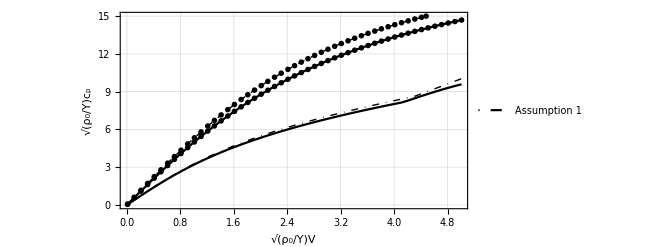

```mathematica
CPLinV=ListPlot[listCpLinV ,PlotLegends->Placed[{"Assumption 2: Linear"},{Left,Top}],LabelStyle->(FontFamily->"Cambria"),Joined->True,PlotRange->{{0,5},{0,15}},GridLines->Automatic,AspectRatio->.5,Frame->{{True,True},{True,True}}, PlotStyle->{Black,Dashed,Thick},FrameLabel->{{"√(ρ_0/Y)c_p",None},{"√(ρ_0/Y)V",None}},PlotMarkers->{ "●",Medium}];
CPFV=ListPlot[listCpFV ,PlotLegends->Placed[{"Assumption 2"},{Left,Top}],LabelStyle->(FontFamily->"Cambria"),Joined->True,PlotRange->{{0,5},{0,15}},GridLines->Automatic,AspectRatio->.5,Frame->{{True,True},{True,True}}, PlotStyle->Black,FrameLabel->{{"√(ρ_0/Y)c_p",None},{"√(ρ_0/Y)V",None}},PlotMarkers->{ "⋆",Large}];
CPH=ListPlot[listCph ,PlotLegends->Placed[{"Assumption 1"},{Right,Bottom}],LabelStyle->(FontFamily->"Cambria"),Joined->True,PlotRange->{{0,5},{0,15}},GridLines->Automatic,AspectRatio->.5,Frame->{{True,True},{True,True}}, PlotStyle->{Black,DotDashed,Thick},FrameLabel->{{"√(ρ_0/Y)c_p",None},{"√(ρ_0/Y)V",None}}];
CPHINE=ListPlot[listCpInE,PlotLegends->Placed[{"Assumption 1: In. El."},{Left,Top}],LabelStyle->(FontFamily->"Cambria"),Joined->True,PlotRange->{{0,5},{0,15}},GridLines->Automatic,AspectRatio->.5,Frame->{{True,True},{True,True}}, PlotStyle->Black,FrameLabel->{{"√(ρ_0/Y)c_p",None},{"√(ρ_0/Y)V",None}}];
Show[CPFV,CPLinV,CPH,CPHINE]
```

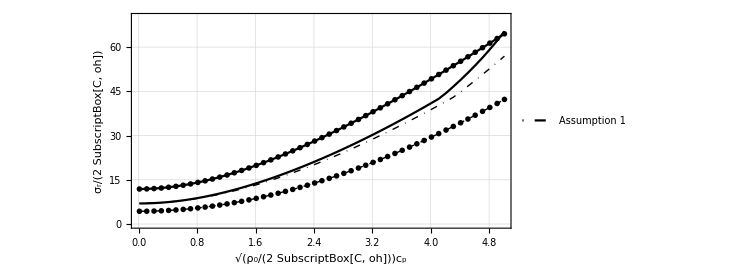

```mathematica
SLinV=ListPlot[listSLinV ,PlotLegends->Placed[{"Assumption 2: Linear"},{Left,Top}],LabelStyle->(FontFamily->"Cambria"),Joined->True,PlotRange->{{0,5},{0,70}},GridLines->Automatic,AspectRatio->.5,Frame->{{True,True},{True,True}}, PlotStyle->{Black,Dashed,Thick},FrameLabel->{{"σ_r/(2 SubscriptBox[C, oh])",None},{"√(ρ_0/(2 SubscriptBox[C, oh]))c_p",None}},PlotMarkers->{ "●",Medium}];
SFV=ListPlot[listSFV ,PlotLegends->Placed[{"Assumption 2"},{Left,Top}],LabelStyle->(FontFamily->"Cambria"),Joined->True,PlotRange->{{0,5},{0,70}},GridLines->Automatic,AspectRatio->.5,Frame->{{True,True},{True,True}}, PlotStyle->Black,FrameLabel->{{"σ_r/(2 SubscriptBox[C, oh])",None},{"√(ρ_0/(2 SubscriptBox[C, oh]))c_p",None}},PlotMarkers->{ "⋆",Large}];
SH=ListPlot[listSh ,PlotLegends->Placed[{"Assumption 1"},{Right,Bottom}],LabelStyle->(FontFamily->"Cambria"),Joined->True,PlotRange->{{0,5},{0,70}},GridLines->Automatic,AspectRatio->.5,Frame->{{True,True},{True,True}}, PlotStyle->{Black,DotDashed,Thick},FrameLabel->{{"σ_r/(2 SubscriptBox[C, oh])",None},{"√(ρ_0/(2 SubscriptBox[C, oh]))c_p",None}}];
SHINE=ListPlot[listSInE,PlotLegends->Placed[{"Assumption 1: In. El."},{Left,Top}],LabelStyle->(FontFamily->"Cambria"),Joined->True,PlotRange->{{0,5},{0,70}},GridLines->Automatic,AspectRatio->.5,Frame->{{True,True},{True,True}}, PlotStyle->Black,FrameLabel->{{"σ_r/(2 SubscriptBox[C, oh])",None},{"√(ρ_0/(2 SubscriptBox[C, oh]))c_p",None}}];
Show[SLinV,SFV,SH,SHINE]
```

# Penetration

# Geometry of the probe

```mathematica
a=0.156/2;(*M= 162+55.3;*);M=162;
Vp=520;μ=0;
CRH=6;
s=2 a CRH;θo=ArcSin[(s-a)/s];
```

# Assumption 1

Curve fitting for Assumption 1  (Hydrostat model)

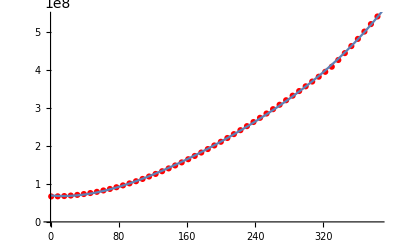

```mathematica
listSh2=listSh;
listSh2[[All,1]]=listSh2[[All,1]]/(√(ρ/Y));
listSh2[[All,2]]=listSh2[[All,2]]Y;
fith = Fit[listSh2, {1,x,x^2,x^3,x^4}, x];
g[x_]:=fith
Show[ListPlot[listSh2, PlotStyle->Red], Plot[ g[x] ,{x, 0, 500}]]
SIGMAFh[vp_,ϕ_]:= fith/.x-> vp Cos[ϕ];(*V=vp Cos[ϕ]*)
```

Curve fitting maximum error and coefficient of determination

```mathematica
R2=0;sstot=0;ssres=0;sum=0;error={};Do[sum=sum+listSh2[[i,2]],{i,1,Dimensions[listSh2][[1]]}];ave=sum/(Dimensions[listSh2][[1]]);Do[sstot=sstot+(listSh2[[i,2]]-ave)^2;val=(fith/.x-> listSh2[[i,1]]);error=Append[error,Abs[listSh2[[i,2]]-val]/Abs[listSh2[[i,2]]]];ssres=ssres+(listSh2[[i,2]]-val)^2,{i,1,Dimensions[listSh2][[1]]}];
R2=1-ssres/sstot;
maxerror=Max[error] 100;
Print["coefficient of determination=",R2,"     Maximum Error=",maxerror,"%"]
```

coefficient of determination=0.999867     Maximum Error=3.86776%

Penetration Time (Tf) and Penetration depth (Zf) without the pusher plate with different friction

```mathematica
M= 162;Clear[μ];
Do[dah=(-SIGMAFh[vp,ϕ])/M(μ Sin[ϕ]+Cos[ϕ])(Sin[ϕ]-(s-a)/s)2 π s^2//FullSimplify;(*Equation 50*)
azh=Integrate[dah,{ϕ,ϕ0,π/2}]/.ϕ0->θo//Simplify;(*Equation 51*)
azhy[v_]:=azh/.vp-> v;dzh=vp/azhy[vp]//Simplify;Zhvp=Integrate[dzh,{vp,Vp0,Vph},Assumptions->1000>Vp0>Vph>0];
Zh[v_,v0_]:=Zhvp/.Vph-> v/.Vp0-> v0;tvp=Integrate[1/azhy[vp],{vp,Vp0,Vph},Assumptions->1000>Vp0>Vph>0];th[v_,v0_]:=tvp/.Vph-> v/.Vp0-> v0;tfhy=th[0,Vp];zfhy=Zh[0,Vp];
Print["μ=",μ,"     Tf=", Round[1000 tfhy,0.1],"ms","     Zf=", Round[zfhy,0.01],"m"],{μ,0,.1,0.01}]
```

μ=0.     Tf=53.1ms     Zf=12.39m

μ=0.01     Tf=50.1ms     Zf=11.71m

μ=0.02     Tf=47.4ms     Zf=11.1m

μ=0.03     Tf=44.9ms     Zf=10.55m

μ=0.04     Tf=42.8ms     Zf=10.06m

μ=0.05     Tf=40.8ms     Zf=9.61m

μ=0.06     Tf=39.ms     Zf=9.19m

μ=0.07     Tf=37.3ms     Zf=8.82m

μ=0.08     Tf=35.8ms     Zf=8.47m

μ=0.09     Tf=34.4ms     Zf=8.14m

μ=0.1     Tf=33.1ms     Zf=7.85m

Adding effects of the pushing plate between t = 0 to 0.003 s

```mathematica
M= 162+55.3;
Do[dah=(-SIGMAFh[vp,ϕ])/M(μ Sin[ϕ]+Cos[ϕ])(Sin[ϕ]-(s-a)/s)2 π s^2//FullSimplify;
azh=Integrate[dah,{ϕ,ϕ0,π/2}]/.ϕ0->θo//Simplify;
azhy[v_]:=azh/.vp-> v;dzh=vp/azhy[vp]//Simplify;tvp=Integrate[1/azhy[vp],{vp,Vp0,Vph},Assumptions->1000>Vp0>Vph>0];th[v_,v0_]:=tvp/.Vph-> v/.Vp0-> v0;
v3ms=FindRoot[th[vv,Vp]-0.003,{vv,Vp}][[1,2]];
Zhvp=Integrate[dzh,{vp,Vp0,Vph},Assumptions->1000>Vp0>Vph>0];
Zh[v_,v0_]:=Zhvp/.Vph-> v/.Vp0-> v0;tfhy=th[0,v3ms]/(162+55.3)(162)+0.003;zfhy=Zh[v3ms,Vp]+Zh[0,v3ms] 162/(162+55.3);
Print["μ=",μ,"     Tf=", Round[1000 tfhy,0.1],"ms","     Zf=", Round[zfhy,0.01],"m"],{μ,0,.1,0.01}]
```

μ=0.     Tf=53.8ms     Zf=12.77m

μ=0.01     Tf=50.8ms     Zf=12.09m

μ=0.02     Tf=48.1ms     Zf=11.49m

μ=0.03     Tf=45.7ms     Zf=10.94m

μ=0.04     Tf=43.5ms     Zf=10.44m

μ=0.05     Tf=41.5ms     Zf=9.99m

μ=0.06     Tf=39.7ms     Zf=9.57m

μ=0.07     Tf=38.1ms     Zf=9.2m

μ=0.08     Tf=36.6ms     Zf=8.85m

μ=0.09     Tf=35.2ms     Zf=8.52m

μ=0.1     Tf=33.9ms     Zf=8.22m

# Assumption 1:Incompressible Elastic Assumption

Curve fitting for Assumption 1 (incompressible elastic )

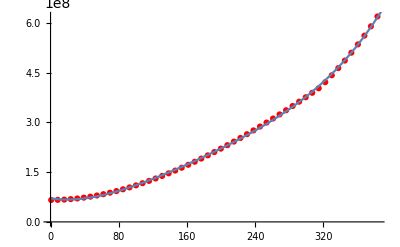

```mathematica
listSInE2=listSInE;
listSInE2[[All,1]]=listSInE2[[All,1]]/(√(ρ/Y));
listSInE2[[All,2]]=listSInE2[[All,2]]Y;
fitInE = Fit[listSInE2, {1,x,x^2,x^3,x^4}, x];
gInE[x_]:=fitInE
Show[ListPlot[listSInE2, PlotStyle->Red], Plot[ gInE[x] ,{x, 0, 500}]]
SIGMAFInE[vp_,ϕ_]:= fitInE/.x-> vp Cos[ϕ];(*V=vp Cos[ϕ]*)
```

Curve fitting maximum error and coefficient of determination

```mathematica
R2=0;sstot=0;ssres=0;sum=0;error={};Do[sum=sum+listSInE2[[i,2]],{i,1,Dimensions[listSInE2][[1]]}];ave=sum/(Dimensions[listSInE2][[1]]);Do[sstot=sstot+(listSInE2[[i,2]]-ave)^2;val=(fitInE/.x-> listSInE2[[i,1]]);error=Append[error,Abs[listSInE2[[i,2]]-val]/Abs[listSInE2[[i,2]]]];ssres=ssres+(listSInE2[[i,2]]-val)^2,{i,1,Dimensions[listSInE2][[1]]}];
R2=1-ssres/sstot;
maxerror=Max[error] 100;
Print["coefficient of determination=",R2,"     Maximum Error=",maxerror,"%"]
```

coefficient of determination=0.999733     Maximum Error=6.85462%

Penetration Time (Tf) and Penetration depth (Zf) without the pusher plate with different friction

```mathematica
M= 162;Clear[μ];
Do[daInE=(-SIGMAFInE[vp,ϕ])/M(μ Sin[ϕ]+Cos[ϕ])(Sin[ϕ]-(s-a)/s)2 π s^2//FullSimplify;(*Equation 50*)
azInE=Integrate[daInE,{ϕ,ϕ0,π/2}]/.ϕ0->θo//Simplify;(*Equation 51*)
azIncE[v_]:=azInE/.vp-> v;dzIncE=vp/azIncE[vp]//Simplify;
ZIncEvp=Integrate[dzIncE,{vp,Vp0,Vph},Assumptions->1000>Vp0>Vph>0];
ZIncE[v_,v0_]:=ZIncEvp/.Vph-> v/.Vp0-> v0;
tIncE=Integrate[1/azIncE[vp],{vp,Vp0,Vph},Assumptions->1000>Vp0>Vph>0];
tFtIncE[v_,v0_]:=tIncE/.Vph-> v/.Vp0-> v0;
tfFInE=tFtIncE[0,Vp];zfFInE=ZIncE[0,Vp];
Print["μ=",μ,"     Tf=", Round[1000 tfFInE,0.1],"ms","     Zf=",  Round[zfFInE,0.01],"m"],{μ,0,.1,0.01}]
```

μ=0.     Tf=52.8ms     Zf=12.23m

μ=0.01     Tf=49.8ms     Zf=11.56m

μ=0.02     Tf=47.1ms     Zf=10.96m

μ=0.03     Tf=44.7ms     Zf=10.42m

μ=0.04     Tf=42.5ms     Zf=9.94m

μ=0.05     Tf=40.6ms     Zf=9.49m

μ=0.06     Tf=38.8ms     Zf=9.09m

μ=0.07     Tf=37.1ms     Zf=8.71m

μ=0.08     Tf=35.6ms     Zf=8.37m

μ=0.09     Tf=34.2ms     Zf=8.05m

μ=0.1     Tf=32.9ms     Zf=7.76m

Adding effects of the pushing plate between t = 0 to 0.003 s

```mathematica
M= 162+55.3;
Do[daInE=(-SIGMAFInE[vp,ϕ])/M(μ Sin[ϕ]+Cos[ϕ])(Sin[ϕ]-(s-a)/s)2 π s^2//FullSimplify;
azInE=Integrate[daInE,{ϕ,ϕ0,π/2}]/.ϕ0->θo//Simplify;
azIncE[v_]:=azInE/.vp-> v;dzIncE=vp/azIncE[vp]//Simplify;
tIncE=Integrate[1/azIncE[vp],{vp,Vp0,Vph},Assumptions->1000>Vp0>Vph>0];
tFtIncE[v_,v0_]:=tIncE/.Vph-> v/.Vp0-> v0;
v3ms=FindRoot[tFtIncE[vv,Vp]-0.003,{vv,Vp}][[1,2]];
ZIncEvp=Integrate[dzIncE,{vp,Vp0,Vph},Assumptions->1000>Vp0>Vph>0];
ZIncE[v_,v0_]:=ZIncEvp/.Vph-> v/.Vp0-> v0;tfFInE=tFtIncE[0,v3ms]/(162+55.3)(162)+0.003;
zfFInE=ZIncE[v3ms,Vp]+ZIncE[0,v3ms] 162/(162+55.3);Print["μ=",μ,"     Tf=", Round[1000 tfFInE,0.1],"ms","     Zf=",  Round[zfFInE,0.01],"m"],{μ,0,.1,0.01}]
```

μ=0.     Tf=53.5ms     Zf=12.61m

μ=0.01     Tf=50.5ms     Zf=11.94m

μ=0.02     Tf=47.9ms     Zf=11.34m

μ=0.03     Tf=45.5ms     Zf=10.81m

μ=0.04     Tf=43.3ms     Zf=10.32m

μ=0.05     Tf=41.3ms     Zf=9.87m

μ=0.06     Tf=39.5ms     Zf=9.47m

μ=0.07     Tf=37.9ms     Zf=9.09m

μ=0.08     Tf=36.4ms     Zf=8.75m

μ=0.09     Tf=35.ms     Zf=8.43m

μ=0.1     Tf=33.7ms     Zf=8.14m

# Assumption 2

Curve fitting for Linear Volumetric model

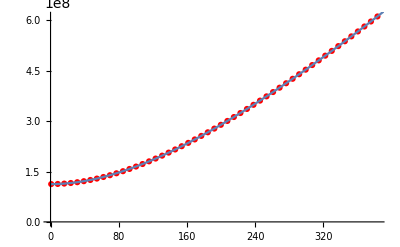

```mathematica
listSFV2=listSFV;
listSFV2[[All,1]]=listSFV2[[All,1]]/(√(ρ/Y));
listSFV2[[All,2]]=listSFV2[[All,2]]Y;
fitFV= Fit[listSFV2, {1,x,x^2,x^3,x^4}, x];
gFV[x_]:=fitFV
Show[ListPlot[listSFV2, PlotStyle->Red], Plot[gFV[x] ,{x, 0, 500}]]
SIGMAFFV[vp_,ϕ_]:= fitFV/.x-> vp Cos[ϕ];(*V=vp Cos[ϕ]*)
```

Curve fitting maximum error and coefficient of determination

```mathematica
R2=0;sstot=0;ssres=0;sum=0;error={};Do[sum=sum+listSFV2[[i,2]],{i,1,Dimensions[listSFV2][[1]]}];ave=sum/(Dimensions[listSFV2][[1]]);Do[sstot=sstot+(listSFV2[[i,2]]-ave)^2;val=(fitFV/.x-> listSFV2[[i,1]]);error=Append[error,Abs[listSFV2[[i,2]]-val]/Abs[listSFV2[[i,2]]]];ssres=ssres+(listSFV2[[i,2]]-val)^2,{i,1,Dimensions[listSFV2][[1]]}];
R2=1-ssres/sstot;
maxerror=Max[error] 100;
Print["coefficient of determination=",R2,"     Maximum Error=",maxerror,"%"]
```

coefficient of determination=1.     Maximum Error=0.106333%

Penetration Time (Tf) and Penetration depth (Zf) without the pusher plate with different friction

```mathematica
M= 162;Clear[μ];
Do[daFV=(-SIGMAFFV[vp,ϕ])/M(μ Sin[ϕ]+Cos[ϕ])(Sin[ϕ]-(s-a)/s)2 π s^2//FullSimplify;(*Equation 50*)
azFV=Integrate[daFV,{ϕ,ϕ0,π/2}]/.ϕ0->θo//Simplify;(*Equation 51*)
azFVN[v_]:=azFV/.vp-> v;dzFV=vp/azFVN[vp]//Simplify;
ZFV=Integrate[dzFV,{vp,Vp0,Vph},Assumptions->1000>Vp0>Vph>0];
ZFVN[v_,v0_]:=ZFV/.Vph-> v/.Vp0-> v0;
tFV=Integrate[1/azFVN[vp],{vp,Vp0,Vph},Assumptions->1000>Vp0>Vph>0];
tFVN[v_,v0_]:=tFV/.Vph-> v/.Vp0-> v0;
tfFV=tFVN[0,Vp];zfFV=ZFVN[0,Vp];
Print["μ=",μ,"     Tf=", Round[1000 tfFV,0.1],"ms","     Zf=",  Round[zfFV,0.01],"m"],{μ,0,.1,0.01}]
```

μ=0.     Tf=32.7ms     Zf=7.79m

μ=0.01     Tf=30.9ms     Zf=7.36m

μ=0.02     Tf=29.2ms     Zf=6.97m

μ=0.03     Tf=27.7ms     Zf=6.62m

μ=0.04     Tf=26.3ms     Zf=6.31m

μ=0.05     Tf=25.1ms     Zf=6.02m

μ=0.06     Tf=24.ms     Zf=5.76m

μ=0.07     Tf=23.ms     Zf=5.52m

μ=0.08     Tf=22.ms     Zf=5.3m

μ=0.09     Tf=21.2ms     Zf=5.09m

μ=0.1     Tf=20.4ms     Zf=4.9m

Adding effects of the pushing plate between t = 0 to 0.003 s

```mathematica
M= 162+55.3;
Do[daFV=(-SIGMAFFV[vp,ϕ])/M(μ Sin[ϕ]+Cos[ϕ])(Sin[ϕ]-(s-a)/s)2 π s^2//FullSimplify;
azFV=Integrate[daFV,{ϕ,ϕ0,π/2}]/.ϕ0->θo//Simplify;
azFVN[v_]:=azFV/.vp-> v;dzFV=vp/azFVN[vp]//Simplify;tFV=Integrate[1/azFVN[vp],{vp,Vp0,Vph},Assumptions->1000>Vp0>Vph>0];tFVN[v_,v0_]:=tFV/.Vph-> v/.Vp0-> v0;
v3ms=FindRoot[tFVN[vv,Vp]-0.003,{vv,Vp}][[1,2]];
ZFV=Integrate[dzFV,{vp,Vp0,Vph},Assumptions->1000>Vp0>Vph>0];
ZFVN[v_,v0_]:=ZFV/.Vph-> v/.Vp0-> v0;tfFV=tFVN[0,v3ms]/(162+55.3)(162)+0.003;
zfFV=ZFVN[v3ms,Vp]+ZFVN[0,v3ms] 162/(162+55.3);
Print["μ=",μ,"     Tf=", Round[1000 tfFV,0.1],"ms","     Zf=",  Round[zfFV,0.01],"m"],{μ,0,.1,0.01}]
```

μ=0.     Tf=33.5ms     Zf=8.17m

μ=0.01     Tf=31.6ms     Zf=7.73m

μ=0.02     Tf=30.ms     Zf=7.35m

μ=0.03     Tf=28.5ms     Zf=7.m

μ=0.04     Tf=27.1ms     Zf=6.68m

μ=0.05     Tf=25.9ms     Zf=6.39m

μ=0.06     Tf=24.8ms     Zf=6.13m

μ=0.07     Tf=23.7ms     Zf=5.89m

μ=0.08     Tf=22.8ms     Zf=5.67m

μ=0.09     Tf=21.9ms     Zf=5.46m

μ=0.1     Tf=21.1ms     Zf=5.27m